# Eletric field of wire and plane

```mathematica
(* Setting *)
(* Assume wire diameter is zero *)
(* wire to plane distance is a *)
```

```mathematica
(* using mirror method *)
```

```mathematica
(* Poisson equation *)
(Grad^2)[V[r]] = - ρ[r]/ϵ0
V[r] = 1/(4π ϵ0)∫ρ[r']/(|r-r'|)(dr')^3
```

```mathematica
(* single wire *)
VLine[k_,a_,x_,y_]:= k/(√((x-a)^2+y^2));
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
ELine[k_,a_,x_,y_]:=Grad[VLine[k,a,x,y],Cartesian[x,y,z]][[{1,2}]]
```

```mathematica
ELine[k,a,x,y]
```

{-(k (-a+x))/(((-a+x)^2+y^2)^(3/2)),-(k y)/(((-a+x)^2+y^2)^(3/2))}

```mathematica
ELine[k1,a,x,y]+ELine[k2,-a,x,y]
```

{-(k1 (-a+x))/(((-a+x)^2+y^2)^(3/2))-(k2 (a+x))/(((a+x)^2+y^2)^(3/2)),-(k1 y)/(((-a+x)^2+y^2)^(3/2))-(k2 y)/(((a+x)^2+y^2)^(3/2))}

```mathematica
Manipulate[
Show[
ContourPlot[VLine[k1,a,x,y]+VLine[k2,-a,x,y],{x,-5,5},{y,-5,5}],
StreamPlot[{-(k1 (-a+x))/(((-a+x)^2+y^2)^(3/2))-(k2 (a+x))/(((a+x)^2+y^2)^(3/2)),-(k1 y)/(((-a+x)^2+y^2)^(3/2))-(k2 y)/(((a+x)^2+y^2)^(3/2))},{x,-5,5},{y,-5,5},StreamPoints->40]
]
,{{k1,-5},-10,10},{{k2,5},-10,10},{{a,1},0,2}]
```

## Periodic wire

```mathematica
(* the wires seperated by b *)
```

```mathematica
(* boundary condition *)
Ey[b/2]==Ey[-b/2]
V[x, b/2] == V[x, -b/2]
```

```mathematica
VLine2[k_,x_,a_,y_,b_]:= k/(√((x-a)^2+(y-b)^2))
```

```mathematica
ELine2[k_,x_,a_,y_,b_]:=Grad[VLine2[k,x,a,y,b],Cartesian[x,y,z]][[{1,2}]]
```

```mathematica
ELine2[k,x,a,y,b]
```

{-(k (-a+x))/(((-a+x)^2+(-b+y)^2)^(3/2)),-(k (-b+y))/(((-a+x)^2+(-b+y)^2)^(3/2))}

```mathematica
EL[k_,x_,a_,y_,b_]:={-(k (-a+x))/(((-a+x)^2+(-b+y)^2)^(3/2)),-(k (-b+y))/(((-a+x)^2+(-b+y)^2)^(3/2))}
```

```mathematica
Manipulate[
Show[
ContourPlot[
VLine2[k1,x,a,y,0]+VLine2[k2,x,-a,y,0]+
VLine2[k1,x,a,y,b]+VLine2[k2,x,-a,y,b]+
VLine2[k1,x,a,y,-b]+VLine2[k2,x,-a,y,-b]+
VLine2[k1,x,a,y,-2b]+VLine2[k2,x,-a,y,-2b]+
VLine2[k1,x,a,y,2b]+VLine2[k2,x,-a,y,2b]+
VLine2[k1,x,a,y,-3b]+VLine2[k2,x,-a,y,-3b]+
VLine2[k1,x,a,y,3b]+VLine2[k2,x,-a,y,3b]
,{x,-1,3},{y,-5,5},AspectRatio->10/4,ImageSize->600],
StreamPlot[EL[k1,x,a,y,0]+EL[k2,x,-a,y,0]+
EL[k1,x,a,y,b]+EL[k2,x,-a,y,b]+
EL[k1,x,a,y,-b]+EL[k2,x,-a,y,-b]+
EL[k1,x,a,y,-2b]+EL[k2,x,-a,y,-2b]+
EL[k1,x,a,y,2b]+EL[k2,x,-a,y,2b]+
EL[k1,x,a,y,-3b]+EL[k2,x,-a,y,-3b]+
EL[k1,x,a,y,3b]+EL[k2,x,-a,y,3b]
,{x,-1,3},{y,-5,5},StreamPoints->Automatic]

]
,{{k1,-5},-10,10},{{k2,5},-10,10},{{a,2},0,2}, {{b,3},4}]
```

```mathematica
VLineS[x_,n_]:=Sum[VLine2[1,x,2,1.5,i 3]+VLine2[-1,x,-2,1.5,i 3], {i,-n,n,1}]
ELines[x_,n_]:=Sum[EL[1,x,2,1.5,3i]+EL[-1,x,-2,1.5,3i], {i,-n,n,1}]
```

```mathematica
Manipulate[
GraphicsGrid[{{
Plot[VLineS[x,n],{x,0,20}],
Plot[ELines[x,n][[1]],{x,0,20},PlotRange->All],
Plot[ELines[x,n][[2]],{x,0,20}]
},{
Plot[VLineS[x,n+1]-VLineS[x,n],{x,0,20}],
Plot[(ELines[x,n+1]-ELines[x,n])[[1]],{x,0,20}],
Plot[(ELines[x,n+1]-ELines[x,n])[[2]],{x,0,20}]
}},ImageSize->700]
,{{n,5},0,50,1}]
```

## Analytic Solution For Periodic Boundary condition

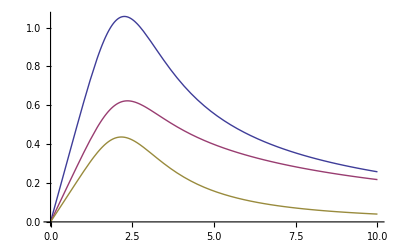

```mathematica
Plot[{VLineS[x,10],VLineS[x,10]-VLineS[x,0],VLineS[x,0]},{x,0,10}]
```

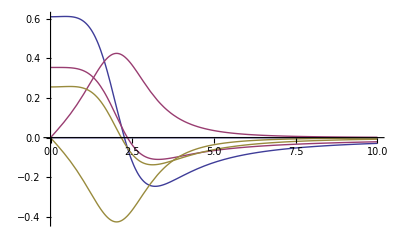

```mathematica
Plot[{ELines[x,10],(ELines[x,10]-ELines[x,0]),ELines[x,0]},{x,0,10},PlotRange->All]
```

```mathematica
D[V[x,y,a,b],y]
```

-(-b+y)/(((-a+x)^2+(-b+y)^2)^(3/2))+(-b+y)/(((a+x)^2+(-b+y)^2)^(3/2))

```mathematica
V[x_,y_,a_,b_]:= 1/(√((x-a)^2+(y-b)^2))-1/(√((x+a)^2+(y-b)^2))
G[y_,b_,n_]:=1/b(y-b/2)+4 π/b Sum[1/i Sin[i 2 π/b(y-b/2)],{i,1,n}]
```

```mathematica
dGy[y_,b_,n_]:=1/b+(4π)/b^2(2π)/b Sum[ Cos[i 2 π/b(y-b/2)],{i,1,n}]
dVy[x_,y_,a_,b_]:=-(-b+y)/(((-a+x)^2+(-b+y)^2)^(3/2))+(-b+y)/(((a+x)^2+(-b+y)^2)^(3/2))
```

```mathematica
Φ[x_,y_,a_,b_,n_]:=V[x,y,a,0]+2 G[y,b,n]/dGy[b/2,b,n] dVy[x,b/2,a,b]
```

```mathematica
Φ[x,y,2,3,n]
```

1/(√((-2+x)^2+y^2))-1/(√((2+x)^2+y^2))-1/(1/3+(8 n π^2)/27)2 (3/(2 (9/4+(-2+x)^2)^(3/2))-3/(2 (9/4+(2+x)^2)^(3/2))) (1/3 (-3/2+y)+2/3 ⅈ ⅇ^(-2/3 ⅈ π (-3/2+y)-(2 ⅈ π y)/3) π (-ⅇ^((2 ⅈ π y)/3) (-ⅇ^(-2/3 ⅈ π y))^n LerchPhi[-ⅇ^(-2/3 ⅈ π y),1,1+n]+ⅇ^(4/3 ⅈ π (-3/2+y)+(2 ⅈ π y)/3) (-ⅇ^((2 ⅈ π y)/3))^n LerchPhi[-ⅇ^((2 ⅈ π y)/3),1,1+n]-ⅇ^(4/3 ⅈ π (-3/2+y)) Log[1+ⅇ^((2 ⅈ π y)/3)]+ⅇ^((4 ⅈ π y)/3) Log[ⅇ^(-2/3 ⅈ π y) (1+ⅇ^((2 ⅈ π y)/3))]))

```mathematica
Manipulate[
Plot[Φ[x,y,2,3,n],{x,-5,5}]
,{n,1,100,1},{y,-1.5,1.5}]
```

```mathematica
Manipulate[
Plot[Φ[x,y,2,3,n],{y,-1.5,1.5}]
,{n,1,100,1},{x,-5,5}]
```

```mathematica
Manipulate[
Plot[y^2],
{n,1,100}]
```